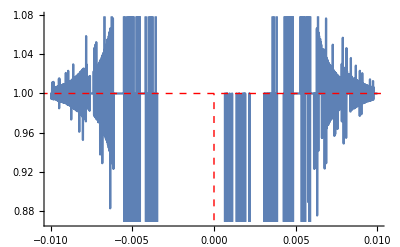
Taylor expansion of (Sin[Tan[x]]-Tan[Sin[x]])/(ArcSin[ArcTan[x]]-ArcTan[ArcSin[x]]) at point 0
-Graphics-
Limit at x = 0 is approx. 1.

```mathematica
(*
  Mathematica 10.0
@Piotr Styczyński 2017
*)

(*
 Function that tries to expand Taylor series of f
and calulate value of f'(x).
Usage: ExpandTaylorAtPoint[fn, x, x0]
	- fn is a function
	- x is a variable that exists in definition of fn, that f will have derivative with respect to it
		- x0 is a point where f' should be calulated

Function generates graphics object, which is a plot of values of
 some Taylor expansion power series.
*)
ExpandTaylorAtPoint[fn_,xName_, x0_]:=Module[{
fnApprox,
fnApproxSeries,
fnApproxAtPoint,
fnApproxValue
},
fnApproxSeries[n_] := Series[fn,{xName ,x0, n}];
fnApprox[n_]:=Normal[fnApproxSeries[n]];
fnApproxAtPoint[n_] := fnApprox[n] /.xName->x0;
fnApproxValue=N[fnApproxAtPoint[15],5];
Framed[Column[{Style[Row[{"Taylor expansion of ",DisplayForm[fn]," at point ", ToString[x0]}],Black,Bold,15, FontFamily-> "Sans Serif"],
GraphicsGrid[{{
Show[
Plot[fn,{xName,x0-0.01,x0+0.01}],
Plot[fnApproxValue,{x,x0-1,x0+1}, PlotStyle->{Red,Dashed,Thin}],
Epilog-> {Directive[{Red,Dashed,Thin}],Line[{{x0,0},{x0,fnApproxValue}}]}
]
}}, ImageSize->Medium],
Style[Row[{"Limit at x = ",ToString[x0]," is approx. ", fnApproxValue}],Black,Bold,15, FontFamily-> "Sans Serif"]
}
]
]
];


(*
  Investigate value of (Sin[Tan[x]]-Tan[Sin[x]])/(ArcSin[ArcTan[x]]-ArcTan[ArcSin[x]]) limit in point 0
*)
ExpandTaylorAtPoint[(Sin[Tan[x]]-Tan[Sin[x]])/(ArcSin[ArcTan[x]]-ArcTan[ArcSin[x]]),x,0]

(*
 Plot is ill-generated, becaouse of 'sloppiness' of a given function near 0
Mentioned sloppiness is caused, by huge absolute values of function derivative in some points.  
*)
```

```mathematica
(*
  Since the function is too sloppy to plot near 0
 we decided to take advantage of Plot options and write our own function.
AccuracyPlot generateds casual plot, but with desired accuracy.

Usage:
	AccuracyPlot[x^2, {x,-1,1}] // Plots quadratin function x^2 like casual plot
	  AccuracyPlot[x^2, {x,-1,1}, Accuracy -> 50] // Plots the same function with increased
                                                   // accuracy of a plot (100 is max, 0 is min)
                                                    // You can sepcify accuracy > 100, but it works
                                                    // but takes a lot of time 
      Other options than Accuracy are: Range (works like normal Plot Range option)
*)
Options[AccuracyPlot]={Accuracy-> 0,Range->Automatic};
AccuracyPlot[fn_,xRng_, OptionsPattern[]]:=Module[{},Framed[Column[{Style[Row[{"Plot of function ",DisplayForm[fn]}],Black,Bold,15, FontFamily-> "Sans Serif"],
GraphicsGrid[{{
Show[
Plot[
fn,
xRng, 
ClippingStyle->Automatic,
PlotRangeClipping->False,
PlotPoints->Max[Min[Ceiling[OptionValue[Accuracy]/100*10000],25000],20], MaxRecursion->Min[Ceiling[OptionValue[Accuracy]/100*3]+2,15],
PlotRange->OptionValue[Range],
PerformanceGoal->"Quality"
]
]
}}, ImageSize->Medium]
}
]
]
];


(*
  Plotting without increased accuracy, gives the same creepy results.
*)
```

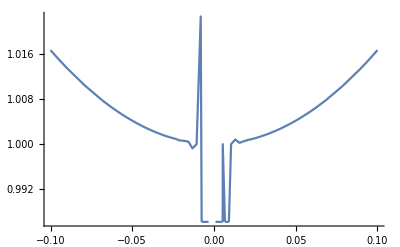
Plot of function (Sin[Tan[x]]-Tan[Sin[x]])/(ArcSin[ArcTan[x]]-ArcTan[ArcSin[x]])
-Graphics-

```mathematica
AccuracyPlot[(Sin[Tan[x]]-Tan[Sin[x]])/(ArcSin[ArcTan[x]]-ArcTan[ArcSin[x]]),{x,-0.1,0.1}]
```

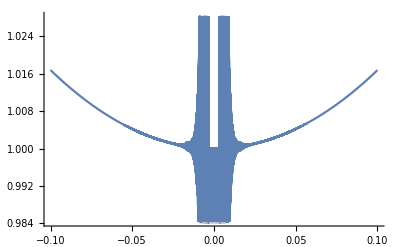
Plot of function (Sin[Tan[x]]-Tan[Sin[x]])/(ArcSin[ArcTan[x]]-ArcTan[ArcSin[x]])
-Graphics-

```mathematica
(*
  Using full power of our function.
The plot finally looks like it should.
*)
AccuracyPlot[(Sin[Tan[x]]-Tan[Sin[x]])/(ArcSin[ArcTan[x]]-ArcTan[ArcSin[x]]),{x,-0.1,0.1},Accuracy->100]
```

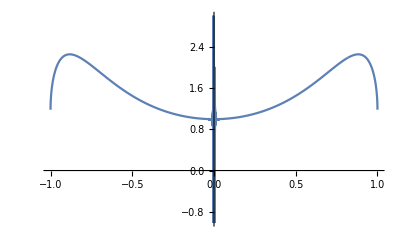
Plot of function (Sin[Tan[x]]-Tan[Sin[x]])/(ArcSin[ArcTan[x]]-ArcTan[ArcSin[x]])
-Graphics-

```mathematica
(*
  Now plotting in bigger interval...
*)
AccuracyPlot[(Sin[Tan[x]]-Tan[Sin[x]])/(ArcSin[ArcTan[x]]-ArcTan[ArcSin[x]]),{x,-1,1},Accuracy->100 ]
```

```mathematica
(*
  Now it works bautifully ^^
*)
```